Wolfram Online Mini Campus. Part 24

Instagram Posts
Pinterest Posts
"Translation" of  📑  SageMath Online Mini Campus. Part 24
http://www.wolfram.com/broadcast/video.php?c=460&v=2672
https://blog.stephenwolfram.com/2019/04/version-12-launches-today-big-jump-for-wolfram-language-and-mathematica/
https://sparse.tamu.edu/

Functions as Creativity Expression

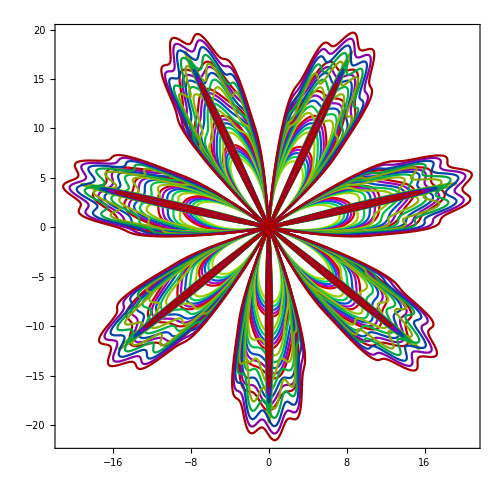

```mathematica
PPIJK=Function[{i,j,k,t},
i*Log[(j+.9Cos[i^2*t])(1.01+Sin[k*t])]];
Show[Table[PolarPlot[PPIJK[i,j,7,t],{t,0,2Pi},
PlotStyle->Darker[Hue[(j-5)/5],.05i]],
{i,3,7},{j,6,10}],PlotRange->All,
ImageSize->500,Frame->True,Axes->False]
```

```mathematica
DynamicModule[{cols,funs},
cols=RGBColor/@{"#3636ff","#ff3636"};
funs[y_,z_]:={{(1-z^4-Abs[y]^1.5)^2,y,z},
{-(1-z^4-Abs[y]^1.5)^2,y,z}};
 Manipulate[Show[Table[ParametricPlot3D[funs[y,z],
 {y,-(1 -z^4)^2,(1-z^4)^2},PlotRange->1,
 Boxed->False,Axes->False,PlotPoints->100,
 SphericalRegion->False,Background->RGBColor["#360036"],
 PlotStyle->Blend[cols,(z+1)/2],ImageSize ->500, 
 ViewPoint->65 {1,0,1},ViewAngle ->Pi/256],
{z,-1+t,1-.001,.1}]],{t,.001,.1}]]
```

```mathematica
CL[k_,n_,alpha_]:=Accumulate[z=1;
Table[z=k*E^(#[[i]]I)z,
{i,n}]]&/@Tuples[{-alpha,alpha},n];
GCL=Function[{k,n,alpha},
Graphics[Table[{ColorData["CherryTones"][i/4],
Rotate[BSplineCurve@Transpose@{Re@#,
Im@#}&/@CL[k,n,alpha],i*Pi/2]},{i,4}],
ImageSize->400,Background->Lighter[Gray,.7]]];
{GCL[.7,10,Pi/4],GCL[.8,8,Pi/6]}
```

{-Graphics-,-Graphics-}

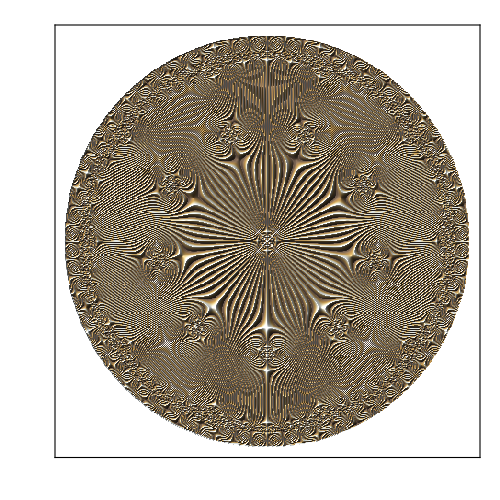

```mathematica
With[{z=x+I y},ReliefPlot[Table[Cos[64#],
{x,##2},{y,##2}]&[If[Abs[z]>1.1 ,
0,#]&@Arg[Sum[(z(z^9+.01))^k!,
{k,4}]],-1.11,1.11,.005],
ImageSize->500,ColorFunction->"CoffeeTones"]]
```

```mathematica
NL=NestList[{Sin[2#1[[2]]]-Cos[3#1[[1]]],
Sin[2#1[[1]]]+Cos[#1[[2]]]}&,{-.5,.5},10^5];
ListPlot[NL,Axes->False,PlotStyle->Opacity[.1],
ColorFunction->Function[{x,y},Hue[x*y]],
ImageSize->500,AspectRatio->1,
Background->Lighter[Gray,.7]]
```

-Graphics-

```mathematica
FP1[x_,k_]:=(.12k*x)^2-12x^2+((.12k)^2-3^1.5*.12k+6)*x;
FP2[k_]:=(.12k)^2-3^0.5*(.12k)-6;
Show[Table[Plot[FP1[x,k]+FP2[k],{x,-2,2},PlotStyle->Hue[k/32],
PlotLegends->Hue[k/32]->.12k],{k,Range[0,31,1]}],
PlotRange->{{-2,2},{-8,2}},Frame->True,GridLines->Automatic,
ImageSize->500,AspectRatio->1,Background->Lighter[Gray,.8]]
```

-Graphics-

Graphics as Creativity Expression

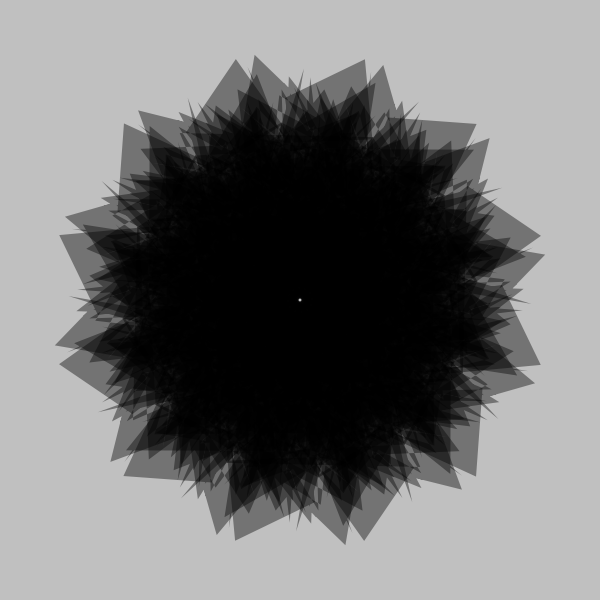

```mathematica
RGS[n_,m_]:=Module[{rt,rm},
rt=RandomReal[{-1,1},{n,2}];rm=RotationMatrix[Pi/m];
Graphics[{Opacity[.4],Style[Polygon[rt.MatrixPower[rm,#]],
ColorData["BrightBands"][1-#/(2m)]]&/@Range[2m]},
Background->RGBColor["silver"],ImageSize->600]];
  RGS[128,6]
```

```mathematica
PPK[a_,b_,c_]:=Module[{ppt,pps},
ppt=Table[{c*Sin[a*t]^2,b*Cos[b*t]^3,
a*Sin[c*t]*Log[t+1]},{t,0,6Pi,.05}];
pps=GeometricTransformation[Tube[ppt,.1],
RotationTransform[Pi,{0, 0, 1}]];
Show[Graphics3D[{FaceForm[{Darker[Gray],Opacity[.3]}],pps}],
Graphics3D[{FaceForm[{Blue,Opacity[.9]}],Tube[ppt,.1]}],
Boxed->False,Background->RGBColor["silver"],
AspectRatio->1,ImageSize->500]];
PPK[4,3,2]
```

-Graphics3D-

```mathematica
PPTS:=Function[{a,b,c},
img=Graphics3D[{RGBColor["#3636ff"],
Tube[Table[{c*Sin[a*t]^2,b*Cos[b*t]^3,
a*Sin[c*t]*Log[t+1]},{t,0,6Pi,.03}],.1]},
Boxed->False,AspectRatio->1,PlotRange->All,
ImageSize->{600,500},Background->RGBColor["silver"]];
ImageCompose[Lighter@Blur[img,10],SetAlphaChannel[img,
ColorNegate[img]],Scaled[{.38,.52}]]]
PPTS[4,3,2]
```

-Graphics-

```mathematica
TK[k_]:={{k,-k,k},{0,0,0},{k,k,k},
{-k,k,k},{-k,-k,k},{k,-k,k},
{k,k,k},{k,k,-k},{-k,k,-k},
{-k,-k,-k},{k,-k,-k},{k,k,-k},
{0,0,0},{k,-k,-k},{k,-k,k}};
Graphics3D[Table[{FaceForm[{ColorData["BrightBands"][.07i],
Opacity[.6]}],Tube[TK[1][[i;;i+1]],.1],
Opacity[1],Sphere[TK[1][[i]],.15]},{i,14}],
Boxed->False,Background->Black,
ViewPoint->{3,-1,0},ImageSize->500]
```

-Graphics3D-

Dimensionality Reduction as Exercises

```mathematica
ExampleData["MachineLearning"]
```

{{MachineLearning,BostonHomes},{MachineLearning,FisherIris},{MachineLearning,MNIST},{MachineLearning,MovieReview},{MachineLearning,Mushroom},{MachineLearning,Satellite},{MachineLearning,Titanic},{MachineLearning,UCILetter},{MachineLearning,WineQuality}}

```mathematica
digits= ExampleData[{"MachineLearning","MNIST"},
"Data"];sample=RandomSample[digits,2000]; 
Delete[digits];sample[[1;;7]]
features=DimensionReduce[sample[[All,1]],2,
Method->"TSNE",PerformanceGoal->"Quality"];
bydigits=GroupBy[Thread[features->sample[[All,2]]],
Last->First];
ListPlot[Values[bydigits],PlotLegends->Keys[bydigits],
ImageSize->600,AspectRatio->1,Frame->True]
```

{-Graphics-→8,-Graphics-→2,-Graphics-→4,-Graphics-→6,-Graphics-→7,-Graphics-→8,-Graphics-→4}

-Graphics-

```mathematica
digits= ExampleData[{"MachineLearning","MNIST"},
"Data"]; sample=RandomSample[digits,3000];
Delete[digits]; sample[[1;;7]]
features=DimensionReduce[sample[[All,1]],
2,Method->"AutoEncoder"];
ListPlot[MapThread[Style[Labeled[#1,#2],
Hue[.1Values[#2]]]&,{features[[1;;320]],
sample[[1;;320]]}],ImageSize->600]
```

{-Graphics-→6,-Graphics-→6,-Graphics-→4,-Graphics-→1,-Graphics-→0,-Graphics-→7,-Graphics-→6}

-Graphics-

Regression as Exercises

```mathematica
train=ExampleData[{"MachineLearning",
"BostonHomes"},"TrainingData"];
test=ExampleData[{"MachineLearning",
"BostonHomes"}, "TestData"];
MLP=NetChain[{LinearLayer[13*4],
BatchNormalizationLayer[],ElementwiseLayer[Ramp],
LinearLayer[512],BatchNormalizationLayer[],
ElementwiseLayer[Ramp],LinearLayer[1]},
"Input"->13,"Output"->"Scalar" ]
results=NetTrain[MLP,train,All,
ValidationSet->test,MaxTrainingRounds->500]
{TrainedMLP,ValLosses}=results[{"TrainedNet",
"ValidationLossList"}]; Min[ValLosses]
```

NetChain[…]

NetTrain Results
summary | ,,  batches:3000  rounds:500  time:6.8s  examples/s:28307
data | ,,  training examples:338  validation examples:168  processed examples:192000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:5.37×10^-1
validation | ,,  loss:1.44×10^1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

12.4007

```mathematica
Predictions= Predict[train,
Method->"GradientBoostedTrees",PerformanceGoal->"Quality"]
testpreds=Predictions[test[[All,1]]];
ListLinePlot[{test[[All,2]],testpreds},ImageSize->600,
PlotLegends->{"Real Data","Predictions"},
PlotLabel->{"Mean Square"->PredictorMeasurements[Predictions,
test,"MeanSquare"]}]
```

PredictorFunction[…]

-Graphics-

Exercises with HTML & D3.js Objects

```mathematica
EmbeddedHTML["<style>svg {background-color:silver;} text {fill:#fff; font-size:135%;} 
.line {fill:none; stroke:#3636ff; stroke-width:2;}             
.grid line, .grid path {stroke:#fff; stroke-opacity:0.9; shape-rendering:crispEdges;}
</style><body><script src='https://d3js.org/d3.v4.min.js'></script><script>
var n=630,m=35,margin={top:m,right:m,bottom:m,left:m},
    width=500-margin.left-margin.right,height=500-margin.top-margin.bottom; 
var xScale=d3.scaleLinear().domain([-2,2]).range([0,width]); 
var yScale=d3.scaleLinear().domain([-2,2]).range([height,0]);
function make_x_gridlines() {return d3.axisBottom(xScale).ticks(11)};
function make_y_gridlines() {return d3.axisLeft(yScale).ticks(11)};            
var data=d3.range(0,n).map(function(i){return {
    'x':Math.cos(0.01*i)+Math.cos(0.11*i)/2+Math.sin(0.3*i)/3,
    'y':Math.sin(0.01*i)+Math.sin(0.11*i)/2+Math.cos(0.3*i)/3}
    })
var lineColor=d3.scaleSequential().domain([0,n]).interpolator(d3.interpolateCool);                       
var svg=d3.select('body').append('svg')
          .attr('width',width+margin.left+margin.right).attr('height',height+margin.top+margin.bottom)
          .append('g').attr('transform','translate('+margin.left+','+margin.top+')');
svg.append('g').attr('class','x axis').call(d3.axisBottom(xScale).tickSize(0.5))
              .attr('transform','translate(0,'+height+')'); 
svg.append('g').attr('class','y axis').call(d3.axisLeft(yScale).tickSize(0.5));    
svg.append('g').attr('class','grid').attr('transform','translate(0,'+height+')')
              .call(make_x_gridlines().tickSize(-height).tickFormat(''));
svg.append('g').attr('class','grid').call(make_y_gridlines().tickSize(-width).tickFormat(''));
var line=d3.line().curve(d3.curveMonotoneX).x(function(d) {return xScale(d.x);})
                                         .y(function(d) {return yScale(d.y);});
svg.append('path').datum(data).attr('class','line').attr('d',line);
</script></body>",ImageSize->{550,550}]
```

Null<style>svg {background-color:silver;…e').attr('d',line);
</script></body><style>svg {background-color:silver;} text {fill:#fff; font-size:135%;} 
.line {fill:none; stroke:#3636ff; stroke-width:2;}             
.grid line, .grid path {stroke:#fff; stroke-opacity:0.9; shape-rendering:crispEdges;}
</style><body><script src='https://d3js.org/d3.v4.min.js'></script><script>
var n=630,m=35,margin={top:m,right:m,bottom:m,left:m},
    width=500-margin.left-margin.right,height=500-margin.top-margin.bottom; 
var xScale=d3.scaleLinear().domain([-2,2]).range([0,width]); 
var yScale=d3.scaleLinear().domain([-2,2]).range([height,0]);
function make_x_gridlines() {return d3.axisBottom(xScale).ticks(11)};
function make_y_gridlines() {return d3.axisLeft(yScale).ticks(11)};            
var data=d3.range(0,n).map(function(i){return {
    'x':Math.cos(0.01*i)+Math.cos(0.11*i)/2+Math.sin(0.3*i)/3,
    'y':Math.sin(0.01*i)+Math.sin(0.11*i)/2+Math.cos(0.3*i)/3}
    })
var lineColor=d3.scaleSequential().domain([0,n]).interpolator(d3.interpolateCool);                       
var svg=d3.select('body').append('svg')
          .attr('width',width+margin.left+margin.right).attr('height',height+margin.top+margin.bottom)
          .append('g').attr('transform','translate('+margin.left+','+margin.top+')');
svg.append('g').attr('class','x axis').call(d3.axisBottom(xScale).tickSize(0.5))
              .attr('transform','translate(0,'+height+')'); 
svg.append('g').attr('class','y axis').call(d3.axisLeft(yScale).tickSize(0.5));    
svg.append('g').attr('class','grid').attr('transform','translate(0,'+height+')')
              .call(make_x_gridlines().tickSize(-height).tickFormat(''));
svg.append('g').attr('class','grid').call(make_y_gridlines().tickSize(-width).tickFormat(''));
var line=d3.line().curve(d3.curveMonotoneX).x(function(d) {return xScale(d.x);})
                                         .y(function(d) {return yScale(d.y);});
svg.append('path').datum(data).attr('class','line').attr('d',line);
</script></body>

```mathematica
EmbeddedHTML["<iframe src='https://olgabelitskaya.github.io/index.html' width='1200' height='200'>
</iframe>",ImageSize->{1250,250}]
```

Null<iframe src='https://olgabelitskaya.g… width='1200' height='200'>
</iframe><iframe src='https://olgabelitskaya.github.io/index.html' width='1200' height='200'>
</iframe>